NDSolveValue::ibcinc: Warning: boundary and initial conditions are inconsistent.

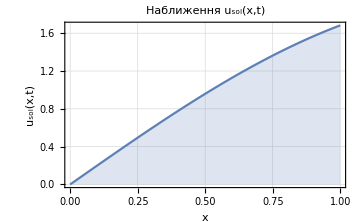
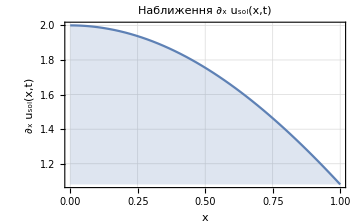

‖u_sol‖_0=1.04437												‖u_sol‖_1=2.

################################################[----FEM n=2 h=1/2 t=0----]################################################

Part::pkspec1: The expression i cannot be used as a part specification.

Part::pkspec1: The expression 1+i cannot be used as a part specification.

Part::pkspec1: The expression i cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

NIntegrate::ncvs: NIntegrate failed to converge near the apparently non-integrable singularity at x = 1..

M=(0.333333 | 0.0833333
0.0833333 | 0.166667)

Part::pkspec1: The expression j cannot be used as a part specification.

Part::pkspec1: The expression 1+j cannot be used as a part specification.

Part::pkspec1: The expression j cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

NIntegrate::ncvs: NIntegrate failed to converge near the apparently non-integrable singularity at x = 1..

A=(4. | -2.
-2. | 2.)

M+Θ*△t*A=(0.533333 | -0.0166667
-0.0166667 | 0.266667)

F={0.23476,0.724091}

q={0.526057,2.74822}

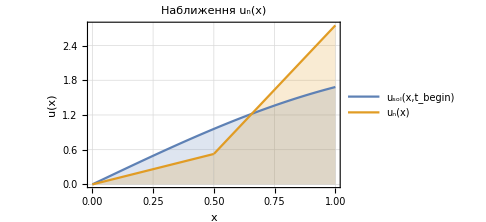
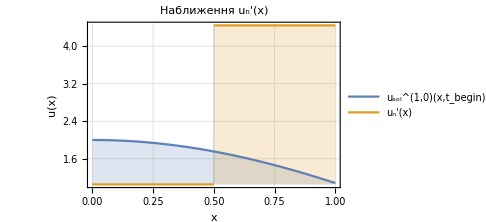

```mathematica
a=0;b=1;deltat = 0.1;
μ[x_]:=1;β[x_]:=0;σ[x_]:=0;
u0 = 0; u1 = Cos[1]; Θ=1/2;
ψ[x_,t_]=1/(t+1)*Sin[x]; ufirst[x_]=Sin[x]+ψ[x,0];
f[x_,t_]:=Sin[x]*(t^2+3*t+1)/(1+t)^2;
Subscript[t, begin]=0;Subscript[t, max]=25;deltat =0.1;
n = 2;
$MaxPiecewiseCases=700;
(*Точний розвязок диф рівняння*)
Subscript[u, sol]=NDSolveValue[{D[u[x,t], t]-(D[μ[x], x]*D[u[x,t], x]+μ[x] *D[u[x,t], x,x])+β[x]* D[u[x,t], x]+σ[x] *u[x,t]==f[x,t],u[0,t]==u0,Derivative[1,0][u][1,t]==u1, u[x,0]==ufirst[x]},u,{x,a,b},{t,Subscript[t, begin]}];
Subscript[plot1u, sol]=Plot[Subscript[u, sol][x,Subscript[t, begin]],{x,a,b},FrameLabel->{"x ","u_sol(x,t) "},PlotLabel->Style[Framed["Наближення u_sol(x,t)"]],Background->White,Filling->Axis,Frame->True,GridLines->Automatic,PlotRange->All, ImageSize->Medium];
Subscript[plot2u, sol]=Plot[Derivative[1,0][Subscript[u, sol]][x,Subscript[t, begin]],{x,a,b},FrameLabel->{"x ","∂_x u_sol(x,t) "},PlotLabel->Style[Framed["Наближення ∂_x u_sol(x,t)"]],Background->White,Filling->Axis,Frame->True,GridLines->Automatic,PlotRange->All, ImageSize->Medium];
Subscript[norma1u, sol]=√NIntegrate[Subscript[u, sol][x,Subscript[t, begin]]^2,{x,a,b}];
Subscript[norma2u, sol]=√NIntegrate[(Subscript[u, sol][x,Subscript[t, begin]])^2+(Derivative[1,0][Subscript[u, sol]][x,Subscript[t, begin]])^2,{x,a,b}];
Print[Subscript[plot1u, sol], "     ", Subscript[plot2u, sol]];
Print["‖u_sol‖_0=",Subscript[norma1u, sol],"\t\t\t\t\t\t\t\t\t\t\t\t‖u_sol‖_1=", Subscript[norma2u, sol]];
(*Функції Куранта*)
ϕ[x0_,i0_] :=
Module[{x=x0, i=i0, k, m},k=i+1; m=i-1;
Piecewise[{
{Piecewise[{{(x-w⟦m⟧)/(w⟦i⟧-w⟦m⟧), w⟦m⟧≤x≤w⟦i⟧},{(w⟦k⟧-x)/(w⟦k⟧-w⟦i⟧),w⟦i⟧≤x≤w⟦k⟧}, {0,x<w⟦i⟧ || x>w⟦k⟧}}],i≠ 1 && i≠n+1}, 
{Piecewise[{{(w⟦k⟧-x)/(w⟦k⟧-w⟦i⟧),w⟦i⟧≤x≤w⟦k⟧},{0,w⟦k⟧<x≤1}}], i==1},
{Piecewise[{{(x-w⟦m⟧)/(w⟦i⟧-w⟦m⟧), w⟦m⟧≤x≤w⟦i⟧},{0,0≤x<w⟦i⟧}}], i==n+1}
}]];
h = (b-a)/n;
w = Table[a+i*h, {i,0,n}];
Print["################################################[----FEM n=",n," h=",h, " t=",Subscript[t, begin],"----]################################################"];
matrixM = 
SparseArray[{{i_,j_}/;Abs[i-j]≤1->
NIntegrate[(ϕ[x,i+1]*ϕ[x,j+1]),
{x,a,b}, Method->"DoubleExponential"]}, {n,n},0.];
Print["M=",MatrixForm[matrixM]];
matrixA= 
SparseArray[{{i_,j_}/;Abs[i-j]≤1->
NIntegrate[(μ[x]*D[ϕ[x,j+1], x]*D[ϕ[x,i+1], x]+β[x]*D[ϕ[x,j+1], x]*ϕ[x,i+1]+σ[x]*ϕ[x,i+1]*ϕ[x,j+1]),
{x,a,b}, Method->"DoubleExponential"]}, {n,n},0.];
Print["A=",MatrixForm[matrixA]];
matrixTotal = matrixM+Θ*deltat*matrixA;
Print["M+Θ*△t*A=",MatrixForm[matrixTotal]];
F = Table[NIntegrate[f[x,Subscript[t, begin]]*ϕ[x,i+1],{x,a,b}]+u1*μ[b]*ϕ[b,i+1], {i,1,n}];
Print["F=",F];
q = LinearSolve[matrixTotal,F];
Print["q=",q];
Subscript[u, n][x_]:=u0+∑_(i=1)^n q[[i]]*ϕ[x,i+1];
difference1 = Plot[{Subscript[u, sol][x,Subscript[t, begin]], Subscript[u, n][x]}, {x,a,b}, FrameLabel->{"x ","u(x) "},PlotLegends->"Expressions",PlotLabel->Style[Framed["Наближення u_n(x)"]],Background->White,Filling->Axis,Frame->True,GridLines->Automatic,PlotRange->All, ImageSize->Medium];
difference2 = Plot[{Derivative[1,0][Subscript[u, sol]][x,Subscript[t, begin]], Subscript[u, n]'[x]}, {x,a,b}, FrameLabel->{"x ","u(x) "},PlotLegends->"Expressions",PlotLabel->Style[Framed["Наближення u_n'(x)"]],Background->White,Filling->Axis,Frame->True,GridLines->Automatic,PlotRange->All, ImageSize->Medium];
Print[difference1, "  ", difference2];
```